Diffusion model

Input parameters:

Gyromagnetic ratio:

```mathematica
γ=267.513 10^6;
```

Diffusion gradient pulse duration:

```mathematica
δ=15 10^-3;
```

Distance between the pulses (diffusion time):

```mathematica
Δ=40 10^-3;
```

Diffusion gradient amplitude:

```mathematica
g=30 10^-3;
```

Exp parameter:

```mathematica
q=(γ/(2π))δ g
```

19159.2

b-value:

```mathematica
b=N[4 π^2 q^2(Δ-δ/3)]
```

5.07204×10^8

Intracellular diffusion coefficient:

```mathematica
Din = 1.9 10^-9;
```

Water diffusion coefficient at body temperature:

```mathematica
Dw = 3.2 10^-9;
```

Fiber cross-section major/minor axis ratio [13]:

```mathematica
α=ConstantArray[Range[1,.1,-.1],{4}]
Dimensions[α]
```

{{1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1},{1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1},{1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1},{1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1}}

{4,10}

Fiber cross - section major axis :

```mathematica
rl={Range[50*10^-6,95*10^-6,5*10^-6],Range[40*10^-6,75*10^-6,3.75*10^-6],Range[30*10^-6,55*10^-6,2.51*10^-6],Range[20*10^-6,35*10^-6,1.51*10^-6]};
```

```mathematica
Dimensions[rl]
```

{4,10}

Fiber cross-section minor axis:

```mathematica
rs=rl*α;
```

```mathematica
Dimensions[rs]
```

{4,10}

```mathematica
dm={Part[rl+rs,1,1],Part[rl+rs,2,1],Part[rl+rs,3,1],Part[rl+rs,4,1]}
```

{0.0001,0.00008,0.00006,0.00004}

Intracellular compartment volume fraction:

```mathematica
Vin =ConstantArray[Range[0.50,0.99,0.05],{4,10}];
Dimensions[Vin]
```

{4,10,10}

Extracellular volume fraction [6.1] :

```mathematica
Vex=1-Vin;
Dimensions[Vex]
```

{4,10,10}

Collagen volume fraction:

```mathematica
Vcol = ConstantArray[Range[0.5,0.99,0.05],{4,10,10}];
Dimensions[Vcol]
```

{4,10,10,10}

Intracellular compartment mean residence time:

```mathematica
τin =1.1;
```

Extracellular compartment mean residence time:

```mathematica
τex = τin Vex/Vin;
Dimensions[τex ]
```

{4,10,10}

Intracellular compartment T2 time:

```mathematica
T2ex =125 10^-3;
```

Extracellular compartment T2 time:

```mathematica
T2in =32 10^-3;
```

Functions for the apparent diffusion coefficients:

```mathematica
α=rs/rl
```

{{1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1},{1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1},{1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1},{1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1}}

Orientation coefficients L [13]:

```mathematica
Lprl=0;
```

```mathematica
Lprpl =α/(α+1)
```

{{0.5,0.473684,0.444444,0.411765,0.375,0.333333,0.285714,0.230769,0.166667,0.0909091},{0.5,0.473684,0.444444,0.411765,0.375,0.333333,0.285714,0.230769,0.166667,0.0909091},{0.5,0.473684,0.444444,0.411765,0.375,0.333333,0.285714,0.230769,0.166667,0.0909091},{0.5,0.473684,0.444444,0.411765,0.375,0.333333,0.285714,0.230769,0.166667,0.0909091}}

```mathematica
Lprps =1/(α+1)
```

{{0.5,0.526316,0.555556,0.588235,0.625,0.666667,0.714286,0.769231,0.833333,0.909091},{0.5,0.526316,0.555556,0.588235,0.625,0.666667,0.714286,0.769231,0.833333,0.909091},{0.5,0.526316,0.555556,0.588235,0.625,0.666667,0.714286,0.769231,0.833333,0.909091},{0.5,0.526316,0.555556,0.588235,0.625,0.666667,0.714286,0.769231,0.833333,0.909091}}

Diffusion coefficient extracellular [11]:

```mathematica
Dex = Dw (1-Vcol)^(2/3);
Dimensions[Dex]
```

{4,10,10,10}

Apparent diffusion coefficient extracellular (general form) [12]:

```mathematica
Dappex [Dex_, Vin_, L_]:= Dex (1-Vin)^(L/(1-L))
```

Apparent diffusion coefficient extracellular:

parallel

```mathematica
Dappexprl=Dappex[Dex,Vin,Lprl];
Dimensions[Dappexprl]
```

{4,10,10,10}

perpendicular long

```mathematica
Dappexprpl=Dappex[Dex,Vin,Lprpl];
Dimensions[Dappexprpl]
```

{4,10,10,10}

perpendicular short

```mathematica
Dappexprps=Dappex[Dex, Vin, Lprps];
Dimensions[Dappexprps]
```

{4,10,10,10}

Apparent diffusion coefficient intracellular (general form) [9]:

```mathematica
Dappin[Din_, q_,Δ_,r_,b_]:= -1/b Log[2(1-Cos[2π q r])/(2π q r)^2+4(2π q r)^2∑_(n=1)^∞ Exp[-n^2 π^2 Din Δ/r^2] (1-(-1)^n Cos[2π q r])/(((2π q r)^2-(n π)^2)^2)]
```

Apparent diffusion coefficient intracellular:

parallel:

```mathematica
Dappinprl=Din
```

1.9×10^-9

perpendicular long:

```mathematica
Dappinprpl=Re[N[Dappin[Din,q,Δ,rl,b]]];
Dimensions[Dappinprpl]
```

{4,10}

perpendicular short:

```mathematica
Dappinprps=Re[N[Dappin[Din,q,Δ,rs,b]]];
Dimensions[Dappinprps]
```

{4,10}

Modified diffusion coefficients

Intracellular modified diffusion coefficient general form [6.1]:

```mathematica
DinM[Dappin_, Dappex_, τin_,τex_,T2ex_,T2in_, q_]:= 1/2(Dappin+Dappex+1/(4 π^2 q^2)(1/τin+1/τex+1/T2in+1/T2ex))-1/2 Sqrt[(Dappex-Dappin+1/(4 π^2 q^2)(1/τex-1/τin-1/T2in+1/T2ex))^2+1/(4 π^4 q^4 τin τex)]
```

Extracellular modified diffusion coefficient general form [6.2]:

```mathematica
DexM[Dappin_, Dappex_, τin_,τex_,T2ex_,T2in_, q_]:= 1/2(Dappin+Dappex+1/(4 π^2 q^2)(1/τin+1/τex+1/T2in+1/T2ex))+1/2 Sqrt[(Dappex-Dappin+1/(4 π^2 q^2)(1/τex-1/τin-1/T2in+1/T2ex))^2+1/(4 π^4 q^4 τin τex)]
```

Intracellular modified diffusion coefficient:

parallel:

```mathematica
DinMprl=DinM[Dappinprl,Dappexprl,τin,τex,T2ex,T2in,q];
Dimensions[DinMprl]
```

{4,10,10,10}

perpendicular long:

```mathematica
DinMprpl=DinM[Dappinprpl,Dappexprpl,τin,τex,T2ex,T2in,q];
Dimensions[DinMprpl]
```

{4,10,10,10}

perpendicular short:

```mathematica
DinMprps=DinM[Dappinprps,Dappexprps,τin,τex,T2ex,T2in,q];
Dimensions[DinMprps]
```

{4,10,10,10}

Extracellular modified diffusion coefficient:

parallel:

```mathematica
DexMprl=DexM[Dappinprl,Dappexprl,τin,τex,T2ex,T2in,q];
Dimensions[DexMprl]
```

{4,10,10,10}

perpendicular long:

```mathematica
DexMprpl=DexM[Dappinprpl,Dappexprpl,τin,τex,T2ex,T2in,q];
Dimensions[DexMprpl]
```

{4,10,10,10}

perpendicular short:

```mathematica
DexMprps=DexM[Dappinprps,Dappexprps,τin,τex,T2ex,T2in,q];
Dimensions[DexMprps]
```

{4,10,10,10}

Modified volume fraction

Extracellular modified volume fraction general form [7]:

```mathematica
VexM[DexM_,DinM_, Vin_,Vex_, Dappin_, Dappex_, q_,T2in_,T2ex_]:= 1/(DexM-DinM)(Vin(Dappin+1/(4 π^2 q^2 T2in))+Vex(Dappex+1/(4 π^2 q^2 T2ex))-DinM)
```

Intracellular modified volume fraction general form [8]:

```mathematica
VinM[VexM_]:=1-VexM
```

Extracellular modified volume fraction:

parallel:

```mathematica
VexMprl=VexM[DexMprl,DinMprl,Vin, Vex,Dappinprl, Dappexprl,q, T2in, T2ex];
Dimensions[VexMprl]
```

{4,10,10,10}

perpendicular long:

```mathematica
VexMprpl=VexM[DexMprpl,DinMprpl,Vin, Vex,Dappinprpl, Dappexprpl,q, T2in, T2ex];
Dimensions[VexMprpl]
```

{4,10,10,10}

perpendicular short:

```mathematica
VexMprps=VexM[DexMprps,DinMprps,Vin, Vex,Dappinprps, Dappexprps,q, T2in, T2ex];
Dimensions[VexMprps]
```

{4,10,10,10}

Intracellular modified volume fraction:

parallel:

```mathematica
VinMprl=VinM[VexMprl];
Dimensions[VinMprl]
```

{4,10,10,10}

perpendicular long:

```mathematica
VinMprpl=VinM[VexMprpl];
Dimensions[VinMprpl]
```

{4,10,10,10}

perpendicular short:

```mathematica
VinMprps=VinM[VexMprps];
Dimensions[VinMprps]
```

{4,10,10,10}

Signal:

Signal from intracellular compartment general form [5]:

```mathematica
Sintra[q_,t_,DinM_,VinM_]:= VinM Exp[-4 π^2 q^2 t DinM]
```

Signal from extracellular compartment  general form [5]:

```mathematica
Sextra[q_,t_,DexM_,VexM_]:= VexM Exp[-4 π^2 q^2 t DexM]
```

Signal from intracellular compartment:

parallel:

```mathematica
Sintraprl[t_]=Sintra[q,t,DinMprl,VinMprl];
```

perpendicular long:

```mathematica
Sintraprpl[t_]=Sintra[q,t,DinMprpl,VinMprpl];
```

perpendicular short:

```mathematica
Sintraprps[t_]=Sintra[q,t,DinMprps,VinMprps];
```

Signal from extracellular compartment:

parallel:

```mathematica
Sextraprl[t_]=Sextra[q,t,DexMprl,VexMprl];
```

perpendicular long:

```mathematica
Sextraprpl[t_]=Sextra[q,t,DexMprpl,VexMprpl];
```

perpendicular short:

```mathematica
Sextraprps[t_]=Sextra[q,t,DexMprps,VexMprps];
```

Simulated diffusion coefficients:

```mathematica
Subscript[λ, 1]=-1/b Log[(Sintraprl[Δ]+Sextraprl[Δ])/(Sintraprl[0]+Sextraprl[0])];
```

```mathematica
Subscript[λ, 2]=-1/b Log[(Sintraprpl[Δ]+Sextraprpl[Δ])/(Sintraprpl[0]+Sextraprpl[0])];
```

```mathematica
Subscript[λ, 3]=-1/b Log[(Sintraprps[Δ]+Sextraprps[Δ])/(Sintraprps[0]+Sextraprps[0])];
```

```mathematica
Dimensions[Subscript[λ, 1]]
Dimensions[Subscript[λ, 2]]
Dimensions[Subscript[λ, 3]]
```

{4,10,10,10}

{4,10,10,10}

{4,10,10,10}

```mathematica
ADC= 1/3(Subscript[λ, 1]+Subscript[λ, 2]+Subscript[λ, 3]);
Dimensions[ADC]
```

{4,10,10,10}

```mathematica
FA = Sqrt[3/2*((Subscript[λ, 1]- ADC)^2+ (Subscript[λ, 2]- ADC)^2+ (Subscript[λ, 3]- ADC)^2)/(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 3]^2)];
Dimensions[FA];
```

```mathematica
CP = (2(Subscript[λ, 2]-Subscript[λ, 3]))/(Subscript[λ, 1]+Subscript[λ, 2]+Subscript[λ, 3]);
Dimensions[CP]
```

{4,10,10,10}

```mathematica
Plots
```

Plots

```mathematica
Part[Vin,1,1,All]
```

{0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95}

```mathematica
Part[FA,1,1,All,1]
```

{0.182939,0.190187,0.194389,0.195167,0.192072,0.18454,0.171845,0.153022,0.126751,0.0913773}

FA plots:

```mathematica
datafa1=Transpose@{Part[Vin,1,1,All],Part[FA,1,1,All,1]};
datafa2=Transpose@{Part[Vin,2,1,All],Part[FA,2,1,All,1]};
datafa3=Transpose@{Part[Vin,3,1,All],Part[FA,3,1,All,1]};
datafa4=Transpose@{Part[Vin,4,1,All],Part[FA,4,1,All,1]};
```

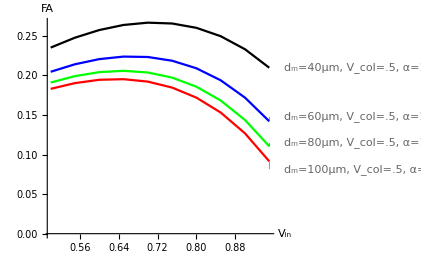

```mathematica
ListPlot[{Labeled[datafa1,"d_m=100μm, V_col=.5, α=1"],Labeled[datafa2,"d_m=80μm, V_col=.5, α=1"],Labeled[datafa3,"d_m=60μm, V_col=.5, α=1"],Labeled[datafa4,"d_m=40μm, V_col=.5, α=1"]}, PlotStyle->{Red,Green,Blue,Black}, Joined->True,AxesLabel->{"V_in","FA"}]
```

```mathematica
FA plots vs alpha:
```

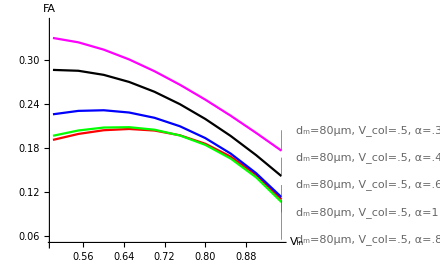

```mathematica
datafa1=Transpose@{Part[Vin,2,1,All],Part[FA,2,1,All,1]};
datafa2=Transpose@{Part[Vin,2,3,All],Part[FA,2,3,All,1]};
datafa3=Transpose@{Part[Vin,2,5,All],Part[FA,2,5,All,1]};
datafa4=Transpose@{Part[Vin,2,7,All],Part[FA,2,7,All,1]};
datafa5=Transpose@{Part[Vin,2,8,All],Part[FA,2,8,All,1]};

ListPlot[{Labeled[datafa1,"d_m=80μm, V_col=.5, α=1"],Labeled[datafa2,"d_m=80μm, V_col=.5, α=.8"],Labeled[datafa3,"d_m=80μm, V_col=.5, α=.6"],Labeled[datafa4,"d_m=80μm, V_col=.5, α=.4"],Labeled[datafa5,"d_m=80μm, V_col=.5, α=.3"]}, PlotStyle->{Red,Green,Blue,Black,Magenta}, Joined->True,AxesLabel->{"V_in","FA"},PlotRange->{0.05,.35}]
```

```mathematica
FA plots vs Vcollagen :
```

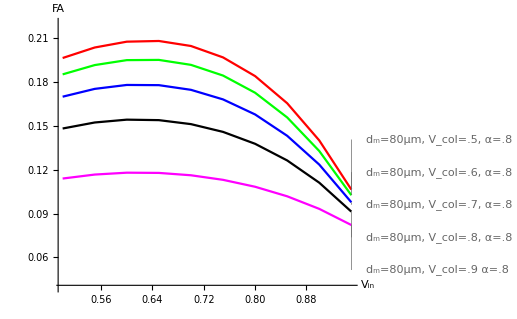

```mathematica
datafa1=Transpose@{Part[Vin,2,1,All],Part[FA,2,3,All,1]};
datafa2=Transpose@{Part[Vin,2,1,All],Part[FA,2,3,All,3]};
datafa3=Transpose@{Part[Vin,2,1,All],Part[FA,2,3,All,5]};
datafa4=Transpose@{Part[Vin,2,1,All],Part[FA,2,3,All,7]};
datafa5=Transpose@{Part[Vin,2,1,All],Part[FA,2,3,All,9]};
ListPlot[{Labeled[datafa1,"d_m=80μm, V_col=.5, α=.8"],Labeled[datafa2,"d_m=80μm, V_col=.6, α=.8"],Labeled[datafa3,"d_m=80μm, V_col=.7, α=.8"],Labeled[datafa4,"d_m=80μm, V_col=.8, α=.8"],Labeled[datafa5,"d_m=80μm, V_col=.9 α=.8"]}, PlotStyle->{Red,Green,Blue,Black,Magenta}, Joined->True,AxesLabel->{"V_in","FA"},PlotRange->{0.04,.22}]
```

```mathematica
Subscript[λ, 1,2,3] plots:
```

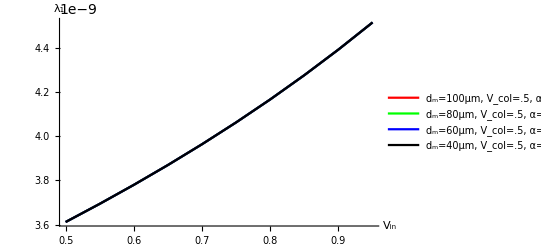

```mathematica
datal1=Transpose@{Part[Vin,1,4,All],Part[Subscript[λ, 1],1,4,All,1]};
datal2=Transpose@{Part[Vin,2,4,All],Part[Subscript[λ, 1],2,4,All,1]};
datal3=Transpose@{Part[Vin,3,4,All],Part[Subscript[λ, 1],3,4,All,1]};
datal4=Transpose@{Part[Vin,4,4,All],Part[Subscript[λ, 1],4,4,All,1]};

ListPlot[{Legended[datal1,"d_m=100μm, V_col=.5, α=.7"],Legended[datal2,"d_m=80μm, V_col=.5, α=.7"],Legended[datal3,"d_m=60μm, V_col=.5, α=.7"],Legended[datal4,"d_m=40μm, V_col=.5, α=.7"]}, PlotStyle->{Red,Green,Blue,Black,Orange,Yellow,Cyan,Magenta}, Joined->True,AxesLabel->{"V_in","λ_1"}]
```

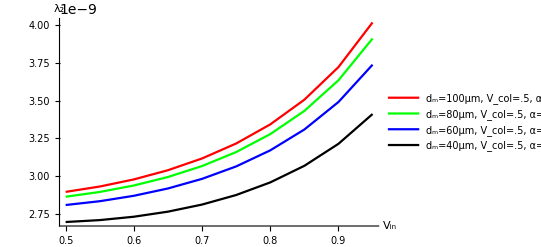

```mathematica
datal1=Transpose@{Part[Vin,1,4,All],Part[Subscript[λ, 2],1,4,All,1]};
datal2=Transpose@{Part[Vin,2,4,All],Part[Subscript[λ, 2],2,4,All,1]};
datal3=Transpose@{Part[Vin,3,4,All],Part[Subscript[λ, 2],3,4,All,1]};
datal4=Transpose@{Part[Vin,4,4,All],Part[Subscript[λ, 2],4,4,All,1]};

ListPlot[{Legended[datal1,"d_m=100μm, V_col=.5, α=.7"],Legended[datal2,"d_m=80μm, V_col=.5, α=.7"],Legended[datal3,"d_m=60μm, V_col=.5, α=.7"],Legended[datal4,"d_m=40μm, V_col=.5, α=.7"]}, PlotStyle->{Red,Green,Blue,Black,Orange,Yellow,Cyan,Magenta}, Joined->True,AxesLabel->{"V_in","λ_2"}]
```

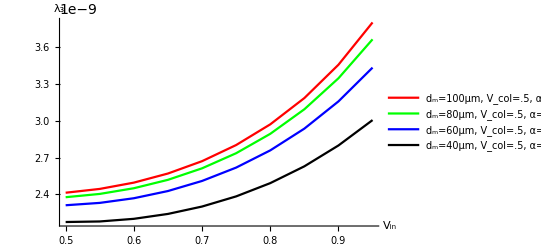

```mathematica
datal1=Transpose@{Part[Vin,1,4,All],Part[Subscript[λ, 3],1,4,All,1]};
datal2=Transpose@{Part[Vin,2,4,All],Part[Subscript[λ, 3],2,4,All,1]};
datal3=Transpose@{Part[Vin,3,4,All],Part[Subscript[λ, 3],3,4,All,1]};
datal4=Transpose@{Part[Vin,4,4,All],Part[Subscript[λ, 3],4,4,All,1]};

ListPlot[{Legended[datal1,"d_m=100μm, V_col=.5, α=.7"],Legended[datal2,"d_m=80μm, V_col=.5, α=.7"],Legended[datal3,"d_m=60μm, V_col=.5, α=.7"],Legended[datal4,"d_m=40μm, V_col=.5, α=.7"]}, PlotStyle->{Red,Green,Blue,Black,Orange,Yellow,Cyan,Magenta}, Joined->True,AxesLabel->{"V_in","λ_3"}]
```

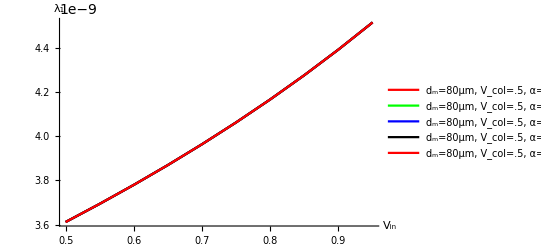

```mathematica
datafa1=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 1],2,1,All,1]};
datafa2=Transpose@{Part[Vin,2,3,All],Part[Subscript[λ, 1],2,3,All,1]};
datafa3=Transpose@{Part[Vin,2,5,All],Part[Subscript[λ, 1],2,5,All,1]};
datafa4=Transpose@{Part[Vin,2,7,All],Part[Subscript[λ, 1],2,7,All,1]};
datafa5=Transpose@{Part[Vin,2,8,All],Part[Subscript[λ, 1],2,8,All,1]};

ListPlot[{Legended[datafa1,"d_m=80μm, V_col=.5, α=1"],Legended[datafa2,"d_m=80μm, V_col=.5, α=.8"],Legended[datafa3,"d_m=80μm, V_col=.5, α=.6"],Legended[datafa4,"d_m=80μm, V_col=.5, α=.4"],Legended[datafa5,"d_m=80μm, V_col=.5, α=.3"]}, PlotStyle->{Red,Green,Blue,Black}, Joined->True,AxesLabel->{"V_in","λ_1"}]
```

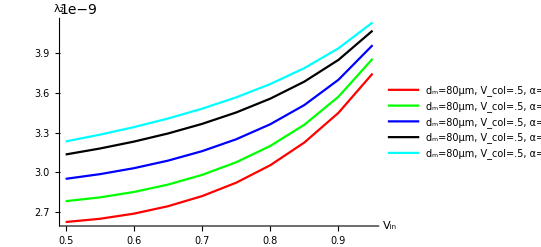

```mathematica
datafa1=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 2],2,1,All,1]};
datafa2=Transpose@{Part[Vin,2,3,All],Part[Subscript[λ, 2],2,3,All,1]};
datafa3=Transpose@{Part[Vin,2,5,All],Part[Subscript[λ, 2],2,5,All,1]};
datafa4=Transpose@{Part[Vin,2,7,All],Part[Subscript[λ, 2],2,7,All,1]};
datafa5=Transpose@{Part[Vin,2,8,All],Part[Subscript[λ, 2],2,8,All,1]};

ListPlot[{Legended[datafa1,"d_m=80μm, V_col=.5, α=1"],Legended[datafa2,"d_m=80μm, V_col=.5, α=.8"],Legended[datafa3,"d_m=80μm, V_col=.5, α=.6"],Legended[datafa4,"d_m=80μm, V_col=.5, α=.4"],Legended[datafa5,"d_m=80μm, V_col=.5, α=.3"]}, PlotStyle->{Red,Green,Blue,Black,Cyan}, Joined->True,AxesLabel->{"V_in","λ_2"}]
```

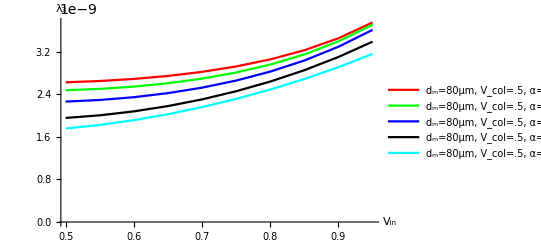

```mathematica
datafa1=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 3],2,1,All,1]};
datafa2=Transpose@{Part[Vin,2,3,All],Part[Subscript[λ, 3],2,3,All,1]};
datafa3=Transpose@{Part[Vin,2,5,All],Part[Subscript[λ, 3],2,5,All,1]};
datafa4=Transpose@{Part[Vin,2,7,All],Part[Subscript[λ, 3],2,7,All,1]};
datafa5=Transpose@{Part[Vin,2,8,All],Part[Subscript[λ, 3],2,8,All,1]};

ListPlot[{Legended[datafa1,"d_m=80μm, V_col=.5, α=1"],Legended[datafa2,"d_m=80μm, V_col=.5, α=.8"],Legended[datafa3,"d_m=80μm, V_col=.5, α=.6"],Legended[datafa4,"d_m=80μm, V_col=.5, α=.4"],Legended[datafa5,"d_m=80μm, V_col=.5, α=.3"]}, PlotStyle->{Red,Green,Blue,Black,Cyan}, Joined->True,AxesLabel->{"V_in","λ_3"}]
```

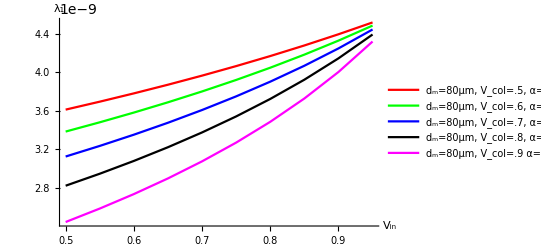

```mathematica
datafa1=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 1],2,3,All,1]};
datafa2=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 1],2,3,All,3]};
datafa3=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 1],2,3,All,5]};
datafa4=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 1],2,3,All,7]};
datafa5=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 1],2,3,All,9]};
ListPlot[{Legended[datafa1,"d_m=80μm, V_col=.5, α=.8"],Legended[datafa2,"d_m=80μm, V_col=.6, α=.8"],Legended[datafa3,"d_m=80μm, V_col=.7, α=.8"],Legended[datafa4,"d_m=80μm, V_col=.8, α=.8"],Legended[datafa5,"d_m=80μm, V_col=.9 α=.8"]}, PlotStyle->{Red,Green,Blue,Black,Magenta}, Joined->True,AxesLabel->{"V_in","λ_1"}]
```

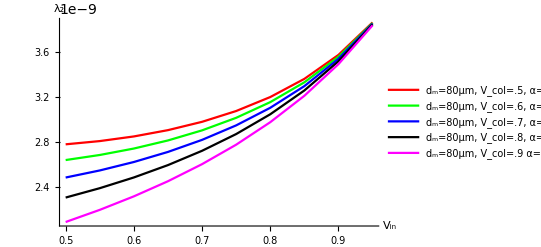

```mathematica
datafa1=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 2],2,3,All,1]};
datafa2=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 2],2,3,All,3]};
datafa3=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 2],2,3,All,5]};
datafa4=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 2],2,3,All,7]};
datafa5=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 2],2,3,All,9]};
ListPlot[{Legended[datafa1,"d_m=80μm, V_col=.5, α=.8"],Legended[datafa2,"d_m=80μm, V_col=.6, α=.8"],Legended[datafa3,"d_m=80μm, V_col=.7, α=.8"],Legended[datafa4,"d_m=80μm, V_col=.8, α=.8"],Legended[datafa5,"d_m=80μm, V_col=.9 α=.8"]}, PlotStyle->{Red,Green,Blue,Black,Magenta}, Joined->True,AxesLabel->{"V_in","λ_2"}]
```

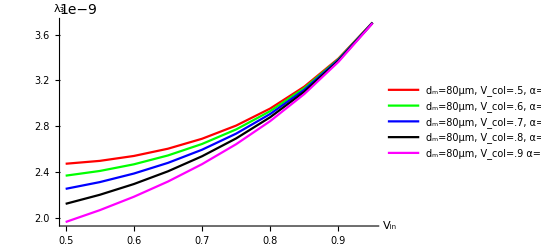

```mathematica
datafa1=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 3],2,3,All,1]};
datafa2=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 3],2,3,All,3]};
datafa3=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 3],2,3,All,5]};
datafa4=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 3],2,3,All,7]};
datafa5=Transpose@{Part[Vin,2,1,All],Part[Subscript[λ, 3],2,3,All,9]};
ListPlot[{Legended[datafa1,"d_m=80μm, V_col=.5, α=.8"],Legended[datafa2,"d_m=80μm, V_col=.6, α=.8"],Legended[datafa3,"d_m=80μm, V_col=.7, α=.8"],Legended[datafa4,"d_m=80μm, V_col=.8, α=.8"],Legended[datafa5,"d_m=80μm, V_col=.9 α=.8"]}, PlotStyle->{Red,Green,Blue,Black,Magenta}, Joined->True,AxesLabel->{"V_in","λ_3"}]
```